```mathematica
Subscript[ϕ, 0]^n/Subscript[ϕ, 0]
```

ϕ_0^(-1+n)

```mathematica
Values={σ^n->{σxn,σyn},Subscript[ϕ, 0]^n->{ϕxn,ϕyn},σ^n1->{σxn1,σyn1},Subscript[ϕ, 0]^n1->{ϕxn1,ϕyn1},
Subscript[ϵ, p]^n->{ϵpxn,ϵpyn},Subscript[ϵ, p]^n1->{ϵpxn1,ϵpyn1},K->{{kxx,kxy},{kyx,kyy}}
};
Numeric={kxx->1000,kxy->0,kyx->0,kyy->500,ϵpxn->0,ϵpyn->0,ϕxn->0,ϕyn->0,epsx1->1/100,epsy1->1/100,alphan->0};
```

```mathematica
Sigma[ϵ_,ϵplastic_]=K.(ϵ-ϵplastic)/.Values
```

{{kxx,kxy},{kyx,kyy}}.(ϵ-ϵplastic)

```mathematica
{σxn,σyn}=Sigma[{epsx,epsy},{ϵpxn,ϵpyn}]
{σxn1,σyn1}=Sigma[{epsx1,epsy1},{ϵpxn1,ϵpyn1}]
```

{kxx (epsx-ϵpxn)+kxy (epsy-ϵpyn),kyx (epsx-ϵpxn)+kyy (epsy-ϵpyn)}

{kxx (epsx1-ϵpxn1)+kxy (epsy1-ϵpyn1),kyx (epsx1-ϵpxn1)+kyy (epsy1-ϵpyn1)}

```mathematica
a[σ_,ϕ_,alpha_]=(σ-ϕ).(σ-ϕ)-alpha
```

-alpha+(σ-ϕ).(σ-ϕ)

```mathematica
NVec[σ_,ϕ_]=2(σ-ϕ)
```

2 (σ-ϕ)

```mathematica
a[σ^n,Subscript[ϕ, 0]^n,alphan]/.Values
```

-alphan+(kxx (epsx-ϵpxn)+kxy (epsy-ϵpyn)-ϕxn)^2+(kyx (epsx-ϵpxn)+kyy (epsy-ϵpyn)-ϕyn)^2

```mathematica
EQEPS=Table[({ϵpxn1,ϵpyn1}-{ϵpxn,ϵpyn}-γ NVec[{σxn1,σyn1},{ϕxn1,ϕyn1}])[[i]]==0,{i,1,2}]
%//MatrixForm
```

{-ϵpxn+ϵpxn1-2 γ (kxx (epsx1-ϵpxn1)+kxy (epsy1-ϵpyn1)-ϕxn1)==0,-ϵpyn+ϵpyn1-2 γ (kyx (epsx1-ϵpxn1)+kyy (epsy1-ϵpyn1)-ϕyn1)==0}

(-ϵpxn+ϵpxn1-2 γ (kxx (epsx1-ϵpxn1)+kxy (epsy1-ϵpyn1)-ϕxn1)==0
-ϵpyn+ϵpyn1-2 γ (kyx (epsx1-ϵpxn1)+kyy (epsy1-ϵpyn1)-ϕyn1)==0)

```mathematica
EQALPHA=alphan1==alphan+γ
```

alphan1==alphan+γ

```mathematica
EQPHI=Table[({ϕxn1,ϕyn1}-{ϕxn,ϕyn}-1/3 γ NVec[{σxn1,σyn1},{ϕxn1,ϕyn1}])[[i]]==0,{i,1,2}]
%//MatrixForm
```

{-ϕxn-2/3 γ (kxx (epsx1-ϵpxn1)+kxy (epsy1-ϵpyn1)-ϕxn1)+ϕxn1==0,-ϕyn-2/3 γ (kyx (epsx1-ϵpxn1)+kyy (epsy1-ϵpyn1)-ϕyn1)+ϕyn1==0}

(-ϕxn-2/3 γ (kxx (epsx1-ϵpxn1)+kxy (epsy1-ϵpyn1)-ϕxn1)+ϕxn1==0
-ϕyn-2/3 γ (kyx (epsx1-ϵpxn1)+kyy (epsy1-ϵpyn1)-ϕyn1)+ϕyn1==0)

```mathematica
EQA = (a[σ^n1,Subscript[ϕ, 0]^n1,alphan1]/.Values)==0
```

-alphan1+(kxx (epsx1-ϵpxn1)+kxy (epsy1-ϵpyn1)-ϕxn1)^2+(kyx (epsx1-ϵpxn1)+kyy (epsy1-ϵpyn1)-ϕyn1)^2==0

```mathematica
Join[{EQA},EQPHI,{EQALPHA},EQEPS]//MatrixForm
variaveis={γ,ϵpxn1,ϵpyn1,ϕxn1,ϕyn1,alphan1}
```

(-alphan1+(kxx (epsx1-ϵpxn1)+kxy (epsy1-ϵpyn1)-ϕxn1)^2+(kyx (epsx1-ϵpxn1)+kyy (epsy1-ϵpyn1)-ϕyn1)^2==0
-ϕxn-2/3 γ (kxx (epsx1-ϵpxn1)+kxy (epsy1-ϵpyn1)-ϕxn1)+ϕxn1==0
-ϕyn-2/3 γ (kyx (epsx1-ϵpxn1)+kyy (epsy1-ϵpyn1)-ϕyn1)+ϕyn1==0
alphan1==alphan+γ
-ϵpxn+ϵpxn1-2 γ (kxx (epsx1-ϵpxn1)+kxy (epsy1-ϵpyn1)-ϕxn1)==0
-ϵpyn+ϵpyn1-2 γ (kyx (epsx1-ϵpxn1)+kyy (epsy1-ϵpyn1)-ϕyn1)==0)

{γ,ϵpxn1,ϵpyn1,ϕxn1,ϕyn1,alphan1}

```mathematica
SOL1 =Solve[EQEPS,{ϕxn1,ϕyn1}][[1]]
```

{ϕxn1→(2 epsx1 kxx γ+2 epsy1 kxy γ+ϵpxn-ϵpxn1-2 kxx γ ϵpxn1-2 kxy γ ϵpyn1)/(2 γ),ϕyn1→(2 epsx1 kyx γ+2 epsy1 kyy γ-2 kyx γ ϵpxn1+ϵpyn-ϵpyn1-2 kyy γ ϵpyn1)/(2 γ)}

```mathematica
EQA2=EQA/.SOL1;
EQPHI2=EQPHI/.SOL1;
EQALPHA2=EQALPHA/.SOL1;
```

```mathematica
SOL2=Solve[EQALPHA2,{alphan1}][[1]]
```

{alphan1→alphan+γ}

```mathematica
EQA3=EQA2/.SOL2;
EQPHI3=EQPHI2/.SOL2;
```

```mathematica
SOL3=Solve[EQPHI3,{ϵpxn1,ϵpyn1}][[1]]
```

{ϵpxn1→-(18 epsx1 kxx γ+18 epsy1 kxy γ+12 epsx1 kxx γ^2+12 epsy1 kxy γ^2-36 epsx1 kxy kyx γ^2+36 epsx1 kxx kyy γ^2+9 ϵpxn+12 γ ϵpxn+18 kyy γ ϵpxn+4 γ^2 ϵpxn+12 kyy γ^2 ϵpxn-18 kxy γ ϵpyn-12 kxy γ^2 ϵpyn-18 γ ϕxn-12 γ^2 ϕxn-36 kyy γ^2 ϕxn+36 kxy γ^2 ϕyn)/(-9-12 γ-18 kxx γ-18 kyy γ-4 γ^2-12 kxx γ^2+36 kxy kyx γ^2-12 kyy γ^2-36 kxx kyy γ^2),ϵpyn1→-(-kyx (epsx1 kxx+epsy1 kxy+ϵpxn/3+ϵpxn/(2 γ)-ϕxn)-(-1/3-kxx-1/(2 γ)) (epsx1 kyx+epsy1 kyy+ϵpyn/3+ϵpyn/(2 γ)-ϕyn))/(kxy kyx-(-1/3-kxx-1/(2 γ)) (-1/3-kyy-1/(2 γ)))}

```mathematica
EQA4=EQA3/.SOL3
```

-alphan-γ+(kxy (epsy1+(-kyx (epsx1 kxx+epsy1 kxy+ϵpxn/3+ϵpxn/(2 γ)-ϕxn)-(-1/3-kxx-1/(2 γ)) (epsx1 kyx+epsy1 kyy+ϵpyn/3+ϵpyn/(2 γ)-ϕyn))/(kxy kyx-(-1/3-kxx-1/(2 γ)) (-1/3-kyy-1/(2 γ))))+kxx (epsx1+(18 epsx1 kxx γ+18 epsy1 kxy γ+12 epsx1 kxx γ^2+12 epsy1 kxy γ^2-36 epsx1 kxy kyx γ^2+36 epsx1 kxx kyy γ^2+9 ϵpxn+12 γ ϵpxn+18 kyy γ ϵpxn+4 γ^2 ϵpxn+12 kyy γ^2 ϵpxn-18 kxy γ ϵpyn-12 kxy γ^2 ϵpyn-18 γ ϕxn-12 γ^2 ϕxn-36 kyy γ^2 ϕxn+36 kxy γ^2 ϕyn)/(-9-12 γ-18 kxx γ-18 kyy γ-4 γ^2-12 kxx γ^2+36 kxy kyx γ^2-12 kyy γ^2-36 kxx kyy γ^2))-1/(2 γ)(2 epsx1 kxx γ+2 epsy1 kxy γ+ϵpxn+(2 kxy γ (-kyx (epsx1 kxx+epsy1 kxy+ϵpxn/3+ϵpxn/(2 γ)-ϕxn)-(-1/3-kxx-1/(2 γ)) (epsx1 kyx+epsy1 kyy+ϵpyn/3+ϵpyn/(2 γ)-ϕyn)))/(kxy kyx-(-1/3-kxx-1/(2 γ)) (-1/3-kyy-1/(2 γ)))+(18 epsx1 kxx γ+18 epsy1 kxy γ+12 epsx1 kxx γ^2+12 epsy1 kxy γ^2-36 epsx1 kxy kyx γ^2+36 epsx1 kxx kyy γ^2+9 ϵpxn+12 γ ϵpxn+18 kyy γ ϵpxn+4 γ^2 ϵpxn+12 kyy γ^2 ϵpxn-18 kxy γ ϵpyn-12 kxy γ^2 ϵpyn-18 γ ϕxn-12 γ^2 ϕxn-36 kyy γ^2 ϕxn+36 kxy γ^2 ϕyn)/(-9-12 γ-18 kxx γ-18 kyy γ-4 γ^2-12 kxx γ^2+36 kxy kyx γ^2-12 kyy γ^2-36 kxx kyy γ^2)+(2 kxx γ (18 epsx1 kxx γ+18 epsy1 kxy γ+12 epsx1 kxx γ^2+12 epsy1 kxy γ^2-36 epsx1 kxy kyx γ^2+36 epsx1 kxx kyy γ^2+9 ϵpxn+12 γ ϵpxn+18 kyy γ ϵpxn+4 γ^2 ϵpxn+12 kyy γ^2 ϵpxn-18 kxy γ ϵpyn-12 kxy γ^2 ϵpyn-18 γ ϕxn-12 γ^2 ϕxn-36 kyy γ^2 ϕxn+36 kxy γ^2 ϕyn))/(-9-12 γ-18 kxx γ-18 kyy γ-4 γ^2-12 kxx γ^2+36 kxy kyx γ^2-12 kyy γ^2-36 kxx kyy γ^2)))^2+(kyy (epsy1+(-kyx (epsx1 kxx+epsy1 kxy+ϵpxn/3+ϵpxn/(2 γ)-ϕxn)-(-1/3-kxx-1/(2 γ)) (epsx1 kyx+epsy1 kyy+ϵpyn/3+ϵpyn/(2 γ)-ϕyn))/(kxy kyx-(-1/3-kxx-1/(2 γ)) (-1/3-kyy-1/(2 γ))))+kyx (epsx1+(18 epsx1 kxx γ+18 epsy1 kxy γ+12 epsx1 kxx γ^2+12 epsy1 kxy γ^2-36 epsx1 kxy kyx γ^2+36 epsx1 kxx kyy γ^2+9 ϵpxn+12 γ ϵpxn+18 kyy γ ϵpxn+4 γ^2 ϵpxn+12 kyy γ^2 ϵpxn-18 kxy γ ϵpyn-12 kxy γ^2 ϵpyn-18 γ ϕxn-12 γ^2 ϕxn-36 kyy γ^2 ϕxn+36 kxy γ^2 ϕyn)/(-9-12 γ-18 kxx γ-18 kyy γ-4 γ^2-12 kxx γ^2+36 kxy kyx γ^2-12 kyy γ^2-36 kxx kyy γ^2))-1/(2 γ)(2 epsx1 kyx γ+2 epsy1 kyy γ+ϵpyn+(-kyx (epsx1 kxx+epsy1 kxy+ϵpxn/3+ϵpxn/(2 γ)-ϕxn)-(-1/3-kxx-1/(2 γ)) (epsx1 kyx+epsy1 kyy+ϵpyn/3+ϵpyn/(2 γ)-ϕyn))/(kxy kyx-(-1/3-kxx-1/(2 γ)) (-1/3-kyy-1/(2 γ)))+(2 kyy γ (-kyx (epsx1 kxx+epsy1 kxy+ϵpxn/3+ϵpxn/(2 γ)-ϕxn)-(-1/3-kxx-1/(2 γ)) (epsx1 kyx+epsy1 kyy+ϵpyn/3+ϵpyn/(2 γ)-ϕyn)))/(kxy kyx-(-1/3-kxx-1/(2 γ)) (-1/3-kyy-1/(2 γ)))+(2 kyx γ (18 epsx1 kxx γ+18 epsy1 kxy γ+12 epsx1 kxx γ^2+12 epsy1 kxy γ^2-36 epsx1 kxy kyx γ^2+36 epsx1 kxx kyy γ^2+9 ϵpxn+12 γ ϵpxn+18 kyy γ ϵpxn+4 γ^2 ϵpxn+12 kyy γ^2 ϵpxn-18 kxy γ ϵpyn-12 kxy γ^2 ϵpyn-18 γ ϕxn-12 γ^2 ϕxn-36 kyy γ^2 ϕxn+36 kxy γ^2 ϕyn))/(-9-12 γ-18 kxx γ-18 kyy γ-4 γ^2-12 kxx γ^2+36 kxy kyx γ^2-12 kyy γ^2-36 kxx kyy γ^2)))^2==0

```mathematica
gammaeq=EQA4[[1]]//.Numeric//N
```

-1. γ+(500. (0.01+5./(-500.333-0.5/γ))-(0.5 (5./(-500.333-0.5/γ)+10. γ+(5000. γ)/(-500.333-0.5/γ)))/γ)^2+(1000. (0.01+(180. γ+180120. γ^2)/(-9.-27012. γ-1.8018×10^7 γ^2))-(0.5 (20. γ+(180. γ+180120. γ^2)/(-9.-27012. γ-1.8018×10^7 γ^2)+(2000. γ (180. γ+180120. γ^2))/(-9.-27012. γ-1.8018×10^7 γ^2)))/γ)^2

```mathematica
gammasubst = (NSolve[gammaeq==0,γ])[[3]]
```

{γ→0.0363317}

```mathematica
completesol=Join[SOL1,SOL2,SOL3,gammasubst]
```

{ϕxn1→(2 epsx1 kxx γ+2 epsy1 kxy γ+ϵpxn-ϵpxn1-2 kxx γ ϵpxn1-2 kxy γ ϵpyn1)/(2 γ),ϕyn1→(2 epsx1 kyx γ+2 epsy1 kyy γ-2 kyx γ ϵpxn1+ϵpyn-ϵpyn1-2 kyy γ ϵpyn1)/(2 γ),alphan1→alphan+γ,ϵpxn1→-(18 epsx1 kxx γ+18 epsy1 kxy γ+12 epsx1 kxx γ^2+12 epsy1 kxy γ^2-36 epsx1 kxy kyx γ^2+36 epsx1 kxx kyy γ^2+9 ϵpxn+12 γ ϵpxn+18 kyy γ ϵpxn+4 γ^2 ϵpxn+12 kyy γ^2 ϵpxn-18 kxy γ ϵpyn-12 kxy γ^2 ϵpyn-18 γ ϕxn-12 γ^2 ϕxn-36 kyy γ^2 ϕxn+36 kxy γ^2 ϕyn)/(-9-12 γ-18 kxx γ-18 kyy γ-4 γ^2-12 kxx γ^2+36 kxy kyx γ^2-12 kyy γ^2-36 kxx kyy γ^2),ϵpyn1→-(-kyx (epsx1 kxx+epsy1 kxy+ϵpxn/3+ϵpxn/(2 γ)-ϕxn)-(-1/3-kxx-1/(2 γ)) (epsx1 kyx+epsy1 kyy+ϵpyn/3+ϵpyn/(2 γ)-ϕyn))/(kxy kyx-(-1/3-kxx-1/(2 γ)) (-1/3-kyy-1/(2 γ))),γ→0.0363317}

```mathematica
{σxn1,σyn1}//.Numeric//.completesol//.Numeric
```

{0.138995,0.137089}

```mathematica
variaveis
variaveis//.completesol//.Numeric
```

{γ,ϵpxn1,ϵpyn1,ϕxn1,ϕyn1,alphan1}

{0.0363317,0.00986101,0.00972582,0.003287,0.00324194,0.0363317}

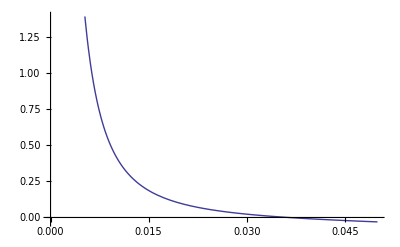

```mathematica
Plot[gammaeq,{γ,0,0.05}]
```

```mathematica
Solve[EQA4,γ]
```

{{γ→Root[-81 alphan+«12»+(32+192 kxx+288 kxx^2-576 kxy kyx-1728 kxx kxy kyx+2592 kxy^2 kyx^2+192 kyy+1152 kxx kyy+1728 kxx^2 kyy-1728 kxy kyx kyy-5184 kxx kxy kyx kyy+288 kyy^2+1728 kxx kyy^2+2592 kxx^2 kyy^2) #1^6&,1]},{γ→Root[-81 alphan+«12»+(32+192 kxx+288 kxx^2-576 kxy kyx-1728 kxx kxy kyx+2592 kxy^2 kyx^2+192 kyy+1152 kxx kyy+1728 kxx^2 kyy-1728 kxy kyx kyy-5184 kxx kxy kyx kyy+288 kyy^2+1728 kxx kyy^2+2592 kxx^2 kyy^2) #1^6&,2]},{γ→Root[-81 alphan+«12»+(32+192 kxx+288 kxx^2-576 kxy kyx-1728 kxx kxy kyx+2592 kxy^2 kyx^2+192 kyy+1152 kxx kyy+1728 kxx^2 kyy-1728 kxy kyx kyy-5184 kxx kxy kyx kyy+288 kyy^2+1728 kxx kyy^2+2592 kxx^2 kyy^2) #1^6&,3]},{γ→Root[-81 alphan+«12»+(32+192 kxx+288 kxx^2-576 kxy kyx-1728 kxx kxy kyx+2592 kxy^2 kyx^2+192 kyy+1152 kxx kyy+1728 kxx^2 kyy-1728 kxy kyx kyy-5184 kxx kxy kyx kyy+288 kyy^2+1728 kxx kyy^2+2592 kxx^2 kyy^2) #1^6&,4]},{γ→Root[-81 alphan+«12»+(32+192 kxx+288 kxx^2-576 kxy kyx-1728 kxx kxy kyx+2592 kxy^2 kyx^2+192 kyy+1152 kxx kyy+1728 kxx^2 kyy-1728 kxy kyx kyy-5184 kxx kxy kyx kyy+288 kyy^2+1728 kxx kyy^2+2592 kxx^2 kyy^2) #1^6&,5]},{γ→Root[-81 alphan+«12»+(32+192 kxx+288 kxx^2-576 kxy kyx-1728 kxx kxy kyx+2592 kxy^2 kyx^2+192 kyy+1152 kxx kyy+1728 kxx^2 kyy-1728 kxy kyx kyy-5184 kxx kxy kyx kyy+288 kyy^2+1728 kxx kyy^2+2592 kxx^2 kyy^2) #1^6&,6]}}